```mathematica
ReadList["d:\\Triangle\\357Data.csv",{Number, Word}]
```

{{0,;10},{1,;756},{2,;757},{3,;3160},{4,;3186},{5,;3187},{6,;3250},{7,;7560},{8,;7561},{9,;7651},{10,;20007},{11,;59548377},{12,;59548401},{13,;45773612811},{14,;45775397187},{15,;2,37617E+14},{16,;2,49919E+16},{17,;2,49919E+16},{18,;2,49919E+16},{19,;2,49919E+16},{20,;2,49919E+16},{21,;2,49919E+16},{22,;2,49919E+16},{23,;2,49919E+16},«132704»,{132728,;1,4601E+133},{132729,;1,4601E+133},{132730,;1,4601E+133},{132731,;1,4601E+133},{132732,;1,4601E+133},{132733,;1,4601E+133},{132734,;1,4601E+133},{132735,;1,4601E+133},{132736,;1,4601E+133},{132737,;1,4601E+133},{132738,;1,4601E+133},{132739,;1,4601E+133},{132740,;1,4601E+133},{132741,;1,4601E+133},{132742,;1,4601E+133},{132743,;1,4601E+133},{132744,;1,4601E+133},{132745,;1,4601E+133},{132746,;1,4601E+133},{132747,;1,4601E+133},{132748,;1,4601E+133},{132749,;1,4601E+133},{132750,;1,4601E+133}}

```mathematica
Plot[ReadList["d:\\Triangle\\357Data.csv",{Number, Word}], {x}]
```

Plot::pllim: Range specification {x} is not of the form {x, xmin, xmax}.

```mathematica
Plot[Table[ReadList["d:\\Triangle\\357Data.csv",{Number,Word}]],{x}]
```

Plot::pllim: Range specification {x} is not of the form {x, xmin, xmax}.

```mathematica
ListPlot[ReadList["d:\\Triangle\\357Data.csv",{Number,Word},10]]
```

-Graphics-

```mathematica
Jef =ReadList["d:\\Triangle\\357Data.csv",{Expression, Expression}, WordSeparators->";"]
```

{{10,756},{757,3160},{3186,3187},{3250,7560},«66369»,{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267001,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267010},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267025,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270006},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270007,EndOfFile}}

```mathematica
Jef.Count
```

{{10,756},{757,3160},{3186,3187},{3250,7560},«66369»,{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267001,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267010},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267025,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270006},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270007,EndOfFile}}.Count

```mathematica
Count[Jef]
```

Count::argtu: Count called with 1 argument; 2 or 3 arguments are expected.

Count[{{10,756},{757,3160},{3186,3187},{3250,7560},«66369»,{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267001,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267010},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267025,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270006},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270007,EndOfFile}}]

```mathematica
Jef
```

{{10,756},{757,3160},{3186,3187},{3250,7560},«66369»,{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267001,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267010},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267025,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270006},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270007,EndOfFile}}

```mathematica
Lijst =ReadList["d:\\Triangle\\Zeroes.txt",{Expression}, WordSeparators->";"]
```

{{10},{756},{757},{3160},{3186},{3187},{3250},«132738»,{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606250260},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267001},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267010},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267025},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270006},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270007}}

```mathematica
ListPlot[Lijst]
```

$Aborted

```mathematica
Kleiner[x_]=Select[Lijst,# > x&;1]
```

{}

```mathematica
Kleiner[1000000]
```

```mathematica
Plot[Select[Lijst,# > x&;1],{x,1,1000}]
```

-Graphics-

```mathematica
Select[Lijst,Function[j]Evaluate[j]> 10000&,1]
```

{}

```mathematica
Lijst
```

{{10},{756},{757},{3160},{3186},{3187},{3250},«132738»,{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606250260},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267001},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267010},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267025},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270006},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270007}}

```mathematica
Select[Lijst,,1]
```

{}

```mathematica
Lijst2 =ReadList["d:\\Triangle\\Zeroes.txt",{Number}, WordSeparators->";"]
```

{{10},{756},{757},{3160},{3186},{3187},{3250},«132738»,{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606250260},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267001},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267010},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267025},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270006},{14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270007}}

```mathematica
Select[Lijst2,# > 1000000&;1]
```

{}

```mathematica
Lijst2 =ReadList["d:\\Triangle\\Zeroes.txt",Number, WordSeparators->";"]
```

{10,756,757,3160,3186,3187,3250,«132738»,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606250260,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267001,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267010,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267025,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270006,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270007}

```mathematica
Select[Lijst2,# > 1000000&,10]
```

{59548377,59548401,45773612811,45775397187,237617431723407,24991943420078301,24991943420078302,24991943420078307,24991943715007536,24991943715007537}

```mathematica
Pick[ReadList["d:\\Triangle\\Zeroes.txt",Number, WordSeparators->";"],{1}]
```

Pick::incomp: Expressions {10, 756, 757, 3160, 3186, 3187, 3250, 7560, 7561, 7651, « 132741 »} and {1} have incompatible shapes.

Pick[{10,756,757,«132745»,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267025,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270006,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270007},{1}]

```mathematica
Lijst2
```

{10,756,757,3160,«132744»,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606267025,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270006,14601381119482439411637521949904493549043119895290521789003512364987639771007850180019396313084473164707610486779753118711135606270007}

```mathematica
LogPlot[ {x  Chance [x,3] Chance [x, 5] Chance [x, 7], Count[Select[Lijst2,# <= x&], _Integer]} ,{x,1, 10^100} ]
```

-Graphics-

```mathematica
Kleiner[x_]=Take[Select[Lijst2,# > x&,1],1]
```

Take::take: Cannot take positions 1 through 1 in {}.

Take[{},1]

```mathematica
Kleiner[1000000]
```

```mathematica
Kleiner[x_] = Select[Lijst2,# > x&,1]
```

{}

```mathematica
Kleiner[1]
```

{}

```mathematica
LogPlot[ { Count[Select[Lijst2,# <= x&] / (x  Chance [x,3] Chance [x, 5] Chance [x, 7]), _Integer]} ,{x,1, 10^100} ]
```

-Graphics-

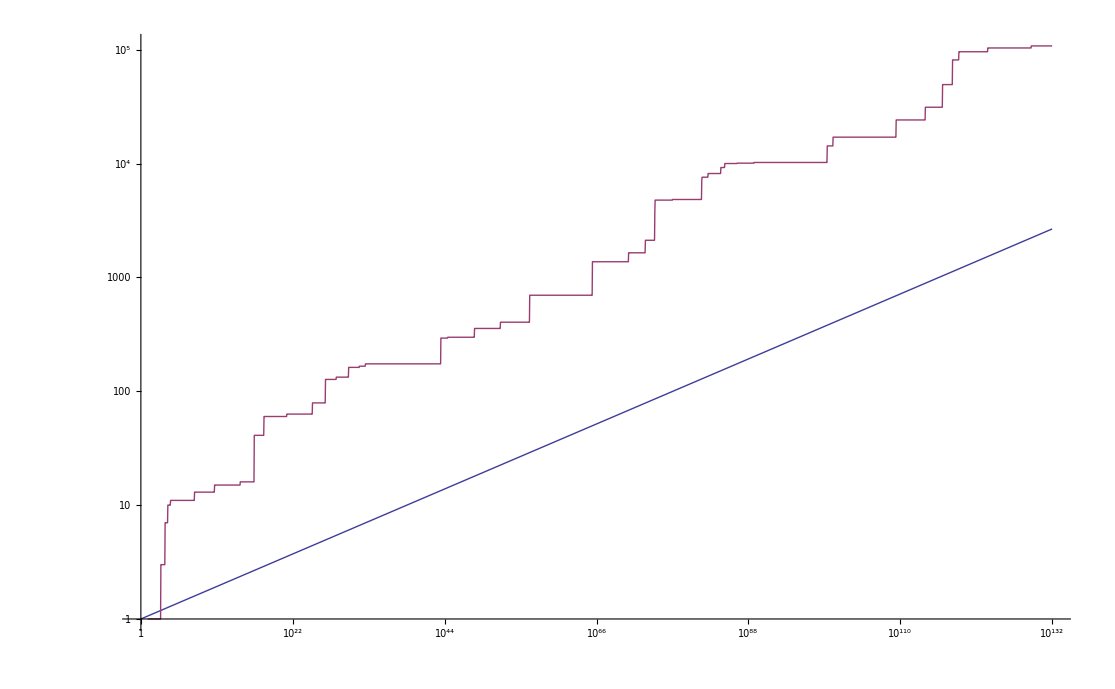

```mathematica
LogLogPlot[ {x  Chance [x,3] Chance [x, 5] Chance [x, 7], Count[Select[Lijst2,# <= x&], _Integer]} ,{x,1, 10^132} ]
```

```mathematica
Drie =ReadList["d:\\Triangle\\Drie.txt",Number, WordSeparators->";"]
```

{0,1,3,4,9,10,12,13,27,28,30,31,36,37,39,40,81,82,84,85,90,91,93,94,108,109,111,112,117,118,120,121,243,244,246,247,252,253,255,256,270,271,273,274,279,280,282,283,324,325,327,328,333,334,336,337,351,352,354,355,360,361,363,364,729,730,732,733,738,739,741,742,756,757,759,«71794»,43757857,43757859,43757860,43758225,43758226,43758228,43758229,43758234,43758235,43758237,43758238,43758252,43758253,43758255,43758256,43758261,43758262,43758264,43758265,43758306,43758307,43758309,43758310,43758315,43758316,43758318,43758319,43758333,43758334,43758336,43758337,43758342,43758343,43758345,43758346,43758468,43758469,43758471,43758472,43758477,43758478,43758480,43758481,43758495,43758496,43758498,43758499,43758504,43758505,43758507,43758508,43758549,43758550,43758552,43758553,43758558,43758559,43758561,43758562,43758576,43758577,43758579,43758580,43758585,43758586,43758588,43758589,43761870,43761871,43761873,43761874,43761879,43761880,43761882,43761883}

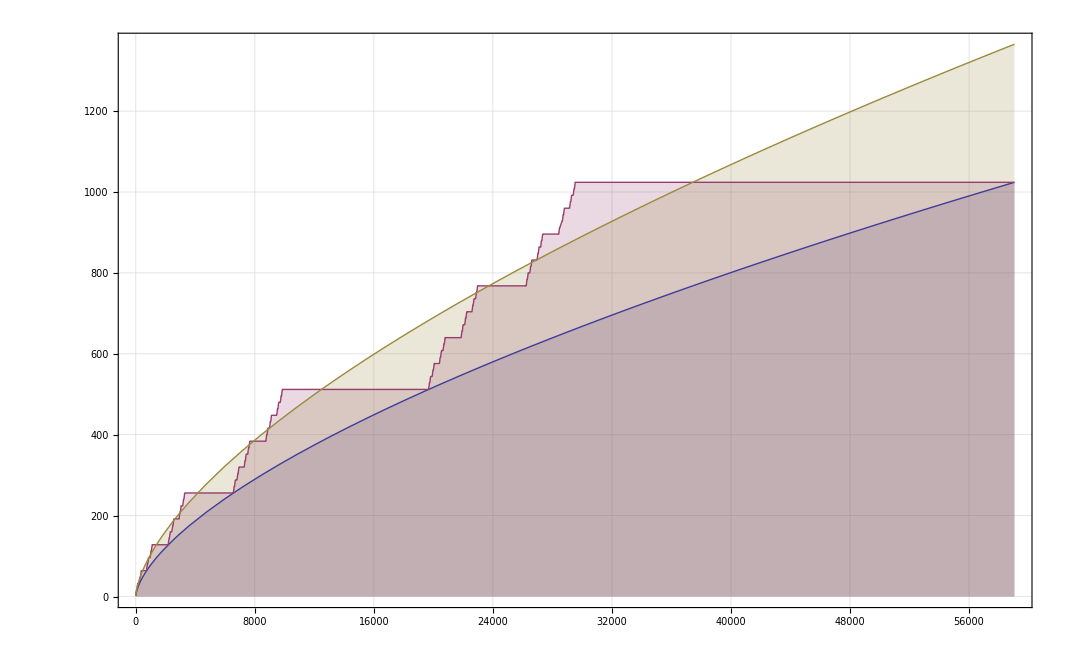

```mathematica
Plot[ {x  Chance [x,3] , Count[Select[Drie,# <= x&], _Integer], 2x  Chance [x *3,3]} ,{x,1,3^10}, GridLines->Automatic, Frame-> True , Filling->Bottom]
```

```mathematica
Binomial[2n,n]
```

Binomial[2 n, n]

```mathematica
2^n
```

2^n

```mathematica
FullSimplify[x Chance [x,3]]
```

(2/3)^(Log[x]/Log[3]) x

```mathematica
x (2/3)^(Subscript[log, 3](x))
```

```mathematica
Chance[x_, n_] = (Floor[(n+1)/2]/(n))^Log[n, x]
```

(Floor[(1+n)/2]/n)^(Log[x]/Log[n])

```mathematica
Chanceb[x_, n_] = (Ceiling[(n+1)/2]/(n))^Log[n, x]
```

(Ceiling[(1+n)/2]/n)^(Log[x]/Log[n])

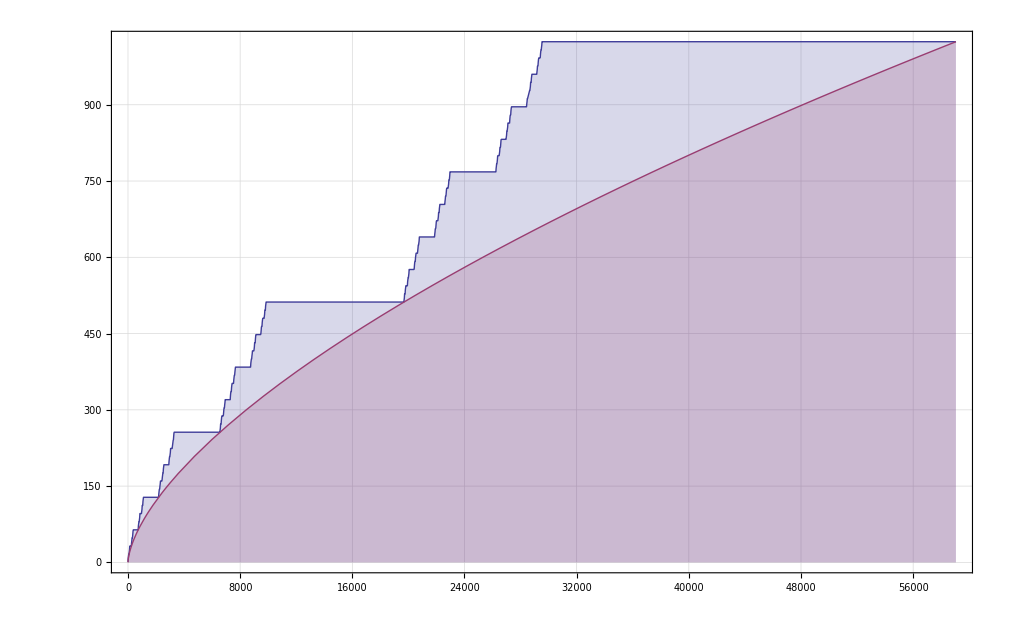

```mathematica
Plot[  { Count[Select[Drie,# <= x&], _Integer], x Chance[x ,3] } ,{x,0,3^10}, GridLines->Automatic, Frame-> True , Filling->Bottom]
```

```mathematica
q= ListInterpolation [{0,2,2,3,3,4,4,4}]
```

InterpolatingFunction[{{1,8}},<>]

```mathematica
q
```

InterpolatingFunction[{{1,8}},<>]

```mathematica
Solve[q]
```

Solve::eqf: InterpolatingFunction[{{1, 8}}, {3, 1, 0, {8}, {4}, 0, 0, 0, 0}, {{1, 2, 3, 4, 5, 6, 7, 8}}, {{0}, {2}, {2}, {3}, {3}, {4}, {4}, {4}}, {Automatic}] is not a well-formed equation.

Solve[InterpolatingFunction[{{1,8}},<>]]